# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Packages

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["Steiner`Utilities`", "packages\\steiner_utilities.wl"]
```

```mathematica
Needs["LeftistHeap`", "packages\\data_structures\\leftist_heap.wl"]
```

```mathematica
Needs["Steiner`Algorithms`GraphUtilities`", "packages\\steiner_algorithms_graph_utilities.wl"]
```

```mathematica
Needs["Steiner`Generator`", "packages\\steiner_generator.wl"]
Needs["Steiner`SteinLib`", "packages\\steiner_steinlib.wl"]
```

```mathematica
Needs["Steiner`Visualization`", "packages\\steiner_visualization.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Exact`", "packages\\steiner_algorithms_exact.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Voronoi`", "packages\\steiner_algorithms_voronoi.wl"]
Needs["Steiner`Algorithms`Approximation`", "packages\\steiner_algorithms_approximation.wl"]
Needs["Steiner`Algorithms`LocalSearch`", "packages\\steiner_algorithms_local_search.wl"]
```

```mathematica
Needs["TestingSystem`", "packages\\testing_system.wl"]
```

## Input data

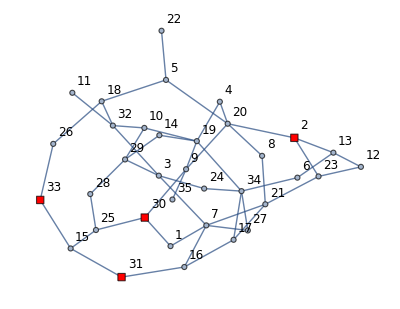

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstanceRG[35, 50, 4, WeightBounds ->{1, 1000}];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12],ImageSize->400]
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_15.mx", {graph15, weightAssociation15, terminals15}];
```

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
```

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstanceRG[150, 250, 20, WeightBounds ->{1, 1000}];
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_100.mx", {graph100, weightAssociation100, terminals100}];
```

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
```

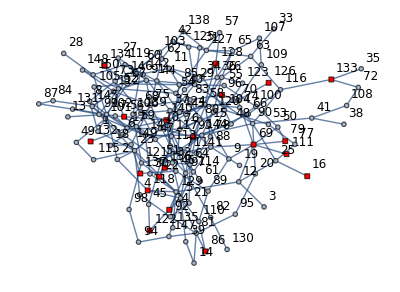

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,12], TerminalSize->1.25, ImageSize->400]
```

```mathematica
getInstancesList["\\steinlib\\D"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["\\steinlib\\D\\d15.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

1000

5000

500

## Visualization Examples

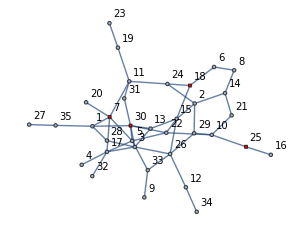

```mathematica
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,10]]
```

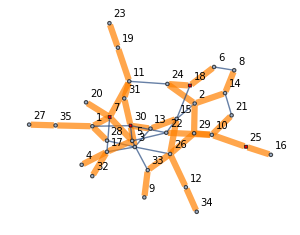

```mathematica
drawGraphSubgraph[graph15, FindSpanningTree[graph15]//EdgeList, terminals15, VertexLabelStyle->Directive[Black,10]]
```

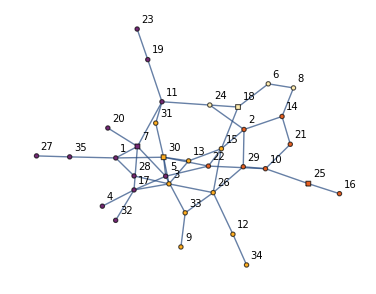

```mathematica
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]]],
TerminalSize->0.65]
```

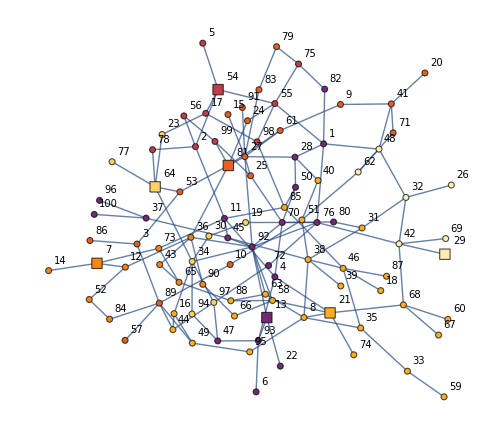

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals100]["voronoi"]]],
TerminalSize->1.25, ImageSize->500]
```

### Animation export

```mathematica
dijkstraVoronoi[graph15, terminals15];
voronoiVertexStyle[VertexList@graph15, Normal[%["voronoi"]]]⟦%["order"]⟧;
a = Table[
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
 VertexStyleFunc->%⟦;;step⟧,
TerminalSize->0.65,
ImageSize->500]
,
{step, 1,VertexCount@graph15, 1}];
```

```mathematica
Export"visual/steiner_voronoi.gif", a, "GIF" , "ControlAppearance"->None,"DisplayDurations"->0.5,ImageSize->700];
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description

```mathematica
-Graphics-
-Graphics-
```

Asymptotic time is : O (3^t n+2^t n^2), where t = #Terminals. n = #Vertices.

#### 15

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
resultDreyfusWagner15
```

{0.154493,Null}

1884.

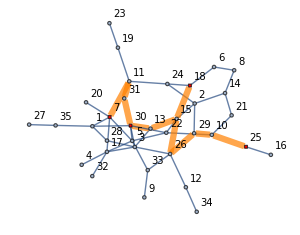
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884.

```mathematica
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

#### 100 Verts

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
resultDreyfusWagner100
```

{13.9607,Null}

5933.

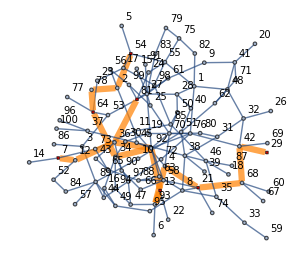
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 5933.

```mathematica
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

#### Stlib

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultDreyfusWagnerStlibTest
```

{0.0491777,Null}

7.

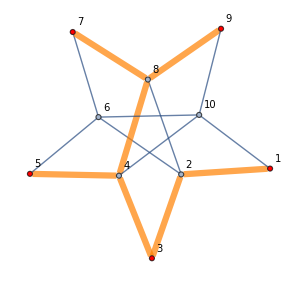
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7.

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagnerStlibTest, stlibTestWeights]
```

7

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### 2-approximation (Mehlhorn) [8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi separation of graph.
	- new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Refind original short-path graph accorgind to spanning tree.
4. Find MinSpanningTree in it.
5. Cut it, to make Steiner-tree.

### Examples

#### 15 Verts

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0072051,Null}

2173

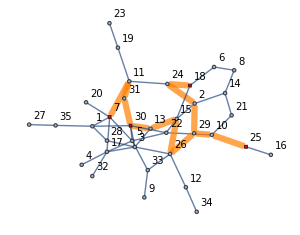
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[treeMehlhorn15, weightAssociation15]
```

{0.0076093,Null}

1884

```mathematica
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884

#### 100 Verts

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{1.01703,Null}

16406

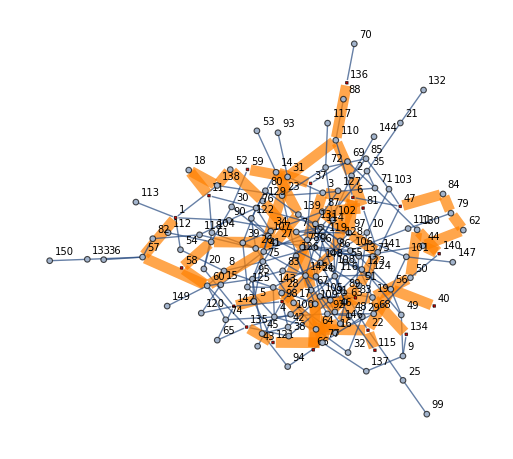
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 16406

```mathematica
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{0.0143318,Null}

6274

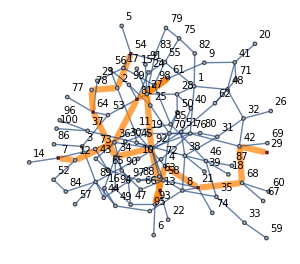
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 6274

```mathematica
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

#### Stlib

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[treeMehlhornStlibTest, stlibTestWeights]
```

{1.46374,Null}

1137

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest];
```

## Greedy algorithms [6][7]

### SPH

### multiple SPH

## Local-search algorithms [7]

Для любого решения T задачи штейнера на графе (не обязательно оптимального) выполняется неравенство MST[V (T)] ≤ T.
Т.е. нахождением минимального остовного дерева набора вершин решения в графе, можно получить тривиальное улучшение решение.
И наоборот, для любого оптимального дерева штейнера должно выполнятся равенство.

### Steiner-Vertex Insertion

Steiner-vertex Insertion просматривает окрестность решений, отличающуюся от данного 1-ой добавленной вершиной, пересчитывает для элементов окрестности MST и проверяет, можно ли получить улучшение таким образом.

```mathematica
tree = steinerVertexInsertion[graph100, treeKouMarkowskyBerman100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{29<->42,42<->68,61<->81,27<->61,36<->81,34<->92,13<->92,34<->64,53<->64,64<->78,27<->53,13<->93,21<->68,4<->21,4<->93,2<->54,2<->78,7<->12,12<->36}

6444

6444

```mathematica
tree = steinerVertexInsertion[stlibTestGraph, treeMehlhornStlibTest];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1125

1137

```mathematica
tree = steinerVertexInsertionFixedPoint[stlibTestGraph, treeMehlhornStlibTest];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1124

1137

```mathematica
tree = steinerVertexInsertion[graph15, treeKouMarkowskyBerman15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{8<->24,10<->24,17<->27,27<->30,16<->30,2<->30,16<->18,10<->18}

3103

3103

### Speed-up

```mathematica
ClearAll[connectingEdgeQ, getConnectingEdges]

connectingEdgeQ[edge_, componentVertices_] :=Xor[MemberQ[componentVertices, First[edge]],MemberQ[componentVertices, Last[edge]]]

getConnectingEdges[edgeList_, componentVertices_] := Select[edgeList, connectingEdgeQ[#, componentVertices]&]
```

```mathematica
ClearAll[findExactEdgePath]

findExactEdgePath[edges_, v_, u_] := UndirectedEdge@@@Partition[FindPath[{1<->2, 2<->3}, 1,3, Infinity, 1]⟦1⟧, 2, 1]
```

```mathematica
ClearAll[steinerVertexInsertion]

steinerVertexInsertion::usage = "";
steinerVertexInsertion[graph_, tree_]:=
Block[{tryAddVertex},
Module[
{treeEdges = EdgeList@tree, treeVertices = VertexList@tree,
graphEdges = EdgeList@graph, graphVertices = VertexList@graph,
edgesByVertex},

edgesByVertex = getConnectingEdges[graphEdges, treeVertices];

(*tryAddVertex[]:=treeEdges;

Scan[
tryAddVertex[IncidenceList[edgesByVertex, #] ]
&,
Complement[graphVertices, treeVertices]]*)

]
]
```

### Steiner-Vertex Elimination

Steiner-vertex Elimination просматривает окрестность решений, отличающуюся от данного 1-ой удаленной вершиной штейнера, и для каждого элемента этой окрестности пересчитывает MST (если он связен), и проверяет, возможно ли улучшение решения.

```mathematica
resultDreyfusWagner15
resultDreyfusWagner100
```

1884.

5933.

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

1884

2173

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{2<->54,2<->78,4<->21,4<->93,7<->12,12<->36,13<->92,13<->93,21<->68,27<->53,27<->61,27<->92,29<->42,36<->81,42<->68,53<->64,61<->81,64<->78}

6221

6444

```mathematica
tree = steinerVertexEliminationFixedPoint[graph100, treeMehlhorn100, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{2<->54,2<->78,4<->21,4<->93,7<->12,12<->36,13<->92,13<->93,21<->68,29<->42,34<->64,34<->92,36<->81,36<->92,42<->68,64<->78}

5933

6274

```mathematica
tree = steinerVertexElimination[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1133

1137

### Speed-up

Это жесть, конечно, в WM писать. Но зато интересные структуры используются: левосторонние кучи, СНМ. Еще можно дописать нормальный поиск lca.

```mathematica
ClearAll[partialKruskal]

partialKruskal[pairsEdgeWeight_List, disj_] := 
Module[{edgeTaken=CreateDataStructure["Stack"]},

Scan[
If[!disj["CommonSubsetQ", First[#⟦1⟧], Last[#⟦1⟧]],
edgeTaken["Insert", #];
disj["Unify", First[#⟦1⟧], Last[#⟦1⟧]];]
&,
 SortBy[pairsEdgeWeight, Last]];

Normal@edgeTaken]
```

```mathematica
ClearAll[walkAndSet]

walkAndSet[graph_, start_, disj_] :=
DepthFirstScan[graph, start,
{"DiscoverVertex"->
((disj["Insert", #];disj["Unify", start, #];)&)}]
```

```mathematica
ClearAll[rootTree]

rootTree[tree_, graphVertexNumber_]:=
Module[{root, depth, parent, children},
root          = First[VertexList@tree];
depth        = CreateDataStructure["FixedArray", graphVertexNumber];
parent      = CreateDataStructure["FixedArray", graphVertexNumber];
children = CreateDataStructure["FixedArray", graphVertexNumber];
Scan[children["SetPart", #, CreateDataStructure["Stack"]]&, VertexList@tree];
DepthFirstScan[EdgeList@tree, root,
{"DiscoverVertex"->
((depth["SetPart", #1, #3];
If[#2≠#1, children["Part", #2]["Push", #1]];
parent["SetPart", #1, #2];)&)}];

{root, depth, parent, children}]
```

```mathematica
ClearAll[steinerVertexEliminationSpeedUp]

steinerVertexEliminationSpeedUp::usage = "";
steinerVertexEliminationSpeedUp[graph_, tree_, terminals_]:=
Block[
{dfs, lheap, lca, lcaUpwards},
With[{treeEdges = EdgeList@tree, treeVertices = VertexList@tree, treeVertexNumber = VertexCount@tree,
graphEdges = EdgeList@graph, graphVertices = VertexList@graph, graphVertNumber = VertexCount[graph]},
Module[
{graphTreeEdges, root,
lcaEdges, depth, parent, children, solution = {-1, treeEdges}},

(* graph rooting *)
{root, depth, parent, children} = rootTree[tree, graphVertNumber];

(* induced by current solution vertices subgraph's edges *)
graphTreeEdges = EdgeList@Subgraph[graph, treeVertices];

(* lca finding *)
lca[v_, u_]:=lcaUpwards[u,  Nest[parent["Part", #]&, v, depth["Part", v] - depth["Part", u]]];
lca[v_, u_]/;depth["Part", v] < depth["Part", u]:=lca[u, v];
lcaUpwards[v_, u_]:=lcaUpwards[parent["Part", v], parent["Part", u]];
lcaUpwards[v_, v_]:=v;

lcaEdges = CreateDataStructure["FixedArray", graphVertNumber];
Scan[lcaEdges["SetPart", #, CreateDataStructure["Stack"]]&, treeVertices];
Scan[lcaEdges["Part", lca[First[#], Last[#]]]["Push", {#, edgeWeight[graph, #]}]&, graphTreeEdges];
Print["Root:"];
Print[root];
Scan[(Print[ToString[#]~~": "];Print[Normal@lcaEdges["Part", #]])&, treeVertices];
(* main step *)
Block[{extractMinUntill, downUpEdgeQ},
Module[{disj,  edgesFinal = {}, mstDisj},
disj = CreateDataStructure["DisjointSet"];

downUpEdgeQ[v_, u_, disj_]:=Xor[disj["MemberQ", v], disj["MemberQ", u]];

extractMinUntill[heapID_]:=
NestWhile[
If[downUpEdgeQ[First@#, Last@#, disj]&[leftistHeapPeek[lheap[heapID]]],
leftistExtractMin[lheap[heapID]],
leftistExtractMin[lheap[heapID]];1]&,
1,
#==1&,
{2,1}];

dfs[v_]:=
Module[
{edgeCandidates, successors =  Normal@children["Part", v]},

If[!MatchQ[successors , {}],
Scan[dfs[#]&, successors];
edgeCandidates = Map[extractMinUntill[#]&, successors];
Print[v];
Print[edgeCandidates];
Print[Normal@lcaEdges["Part", v]];
edgeCandidates =
DeleteCases[
Join[{#, edgeWeight[graph, #]}&/@edgeCandidates, Normal@lcaEdges["Part", v]],
x_/;MemberQ[#, x⟦1⟧]]&[IncidenceList[graphTreeEdges, v]];
Print[edgeCandidates];

mstDisj = disj["Copy"];
If[parent["Part", v]≠v,
walkAndSet[VertexDelete[treeEdges, v], parent["Part", v], mstDisj];
];
(* СНМ !!!*)
edgesFinal = partialKruskal[edgeCandidates, mstDisj];

Sow[{v, edgeCandidates, Union[edgesFinal⟦All, 1⟧, Complement[treeEdges, IncidenceList[treeEdges, v]]]}];

If[FreeQ[terminals, v]∧
ConnectedGraphQ@Graph[Complement[treeVertices, {v}],Union[edgesFinal⟦All, 1⟧, Complement[treeEdges, IncidenceList[treeEdges, v]]]]∧Total[edgesFinal⟦All, 2⟧] < Total[edgeWeight[graph, #]&/@IncidenceList[treeEdges, v]],
solution = {v, Union[edgesFinal⟦All, 1⟧, Complement[treeEdges, IncidenceList[treeEdges, v]]]};];

disj["Insert", v];
Scan[disj["Unify", v, #]&, successors];
lheap[v]=leftistHeapHeapify[{#, edgeWeight[graph, #]}&/@Cases[IncidenceList[graphTreeEdges, v], x_/;Xor[disj["MemberQ", x⟦1⟧], disj["MemberQ", x⟦2⟧]]]];
Map[leftistHeapMeldClearly[lheap[v], lheap[#]]&, successors];

,

(* leaf *)
disj["Insert", v];
Print["Leaf:"];
Print[v];
Print[{IncidenceList[graphTreeEdges, v]}];
Print["end:"];
lheap[v]=leftistHeapHeapify[{#, edgeWeight[graph, #]}&/@IncidenceList[graphTreeEdges, v]];
];
];

dfs[root];
solution
];
];
]
]
]
```

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{0.0442199,Null}

6444

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0098035,Null}

2173

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

34

{2<->54,2<->78,4<->21,4<->93,7<->12,12<->36,13<->92,13<->93,21<->68,27<->53,27<->61,27<->92,29<->42,36<->81,42<->68,53<->64,61<->81,64<->78}

6221

6444

```mathematica
treeTest =  steinerVertexElimination[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[treeTest, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

1884

2173

```mathematica
var = Reap[steinerVertexEliminationSpeedUp[graph15, treeKouMarkowskyBerman15, terminals15], _, First]⟦2, 1⟧
```

```mathematica
IncidenceList[treeKouMarkowskyBerman15, 10]
```

{10<->25,10<->29}

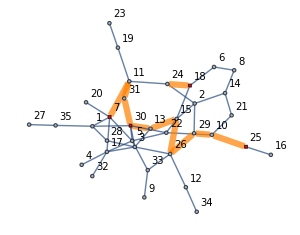
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

```mathematica
gridResult[graph15,  terminals15, {7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,18<->24,26<->29,30<->31}, edgeWeightSum[graph15, treeKouMarkowskyBerman15]]
```

```mathematica
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeKouMarkowskyBerman15]
```

2173

2173

```mathematica
steinerVertexEliminationSpeedUp[graph15, treeKouMarkowskyBerman15, terminals15]
tree =  %⟦2⟧;
%%⟦1⟧;
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeKouMarkowskyBerman15]
%%%%
```

```mathematica
t1 = steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100];//AbsoluteTiming
t2 = steinerVertexEliminationSpeedUp[graph100, treeKouMarkowskyBerman100, terminals100];//AbsoluteTiming
```

{0.0630061,Null}

{0.0346224,Null}

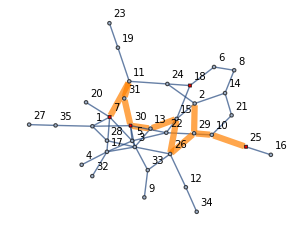
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1404

```mathematica
gridResult[graph15,  terminals15, tree, edgeWeightSum[graph15, tree]]
```

```mathematica
gridResult[graph15,  terminals15, treeTest, edgeWeightSum[graph15, treeKouMarkowskyBerman15]]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, edgeWeightSum[graph15, treeKouMarkowskyBerman15]]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

### VIVE

```mathematica
tree =  steinerVIVEFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

1884

2173

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{2<->54,2<->78,4<->21,4<->93,7<->12,12<->36,13<->92,13<->93,21<->68,27<->53,27<->61,27<->92,29<->42,36<->81,42<->68,53<->64,61<->81,64<->78}

6221

6444

```mathematica
tree = steinerVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1120

1137

### Key-Path Exchange

```mathematica
ClearAll[crucialQ]

crucialQ[v_, tree_, terminals_]:=(VertexDegree[tree, v]≥3)∨(VertexDegree[tree, v] == 2 ∧MemberQ[terminals, v])
```

```mathematica
ClearAll[rootTree]

rootTree[tree_, graphVertexNumber_, terminals_]:=
Module[{root, depth, parent, children},
root          = FirstCase[VertexList@tree, x_/;crucialQ[x, tree, terminals]];
depth        = CreateDataStructure["FixedArray", graphVertexNumber];
parent      = CreateDataStructure["FixedArray", graphVertexNumber];
children = CreateDataStructure["FixedArray", graphVertexNumber];
Scan[children["SetPart", #, CreateDataStructure["Stack"]]&, VertexList@tree];
DepthFirstScan[EdgeList@tree, root,
{"DiscoverVertex"->
((depth["SetPart", #1, #3];
If[#2≠#1, children["Part", #2]["Push", #1]];
parent["SetPart", #1, #2];)&)}];

{root, depth, parent, children}]
```

```mathematica
ClearAll[steinerKeyPathExchange]

steinerKeyPathExchange::usage = "";
steinerKeyPathExchange[graph_, tree_, terminals_]:=
Block[{lheap, dfs, tryEliminatePath,
voronoiRepair, extractMinUntill, downUpEdgeQ,
currentInternalKeyPath=CreateDataStructure["Stack"]},
With[{treeVertexNumber = VertexCount@tree, graphVertexNumber=VertexCount@graph,
treeEdges = EdgeList@tree, graphEdges = EdgeList@graph, treeVertices = VertexList@tree},
Module[{voronoi, dist, anc, cent, heapArray, solution,
root, depth, parent, children,graphTreeEdges,
disj},

solution = treeEdges;
graphTreeEdges = EdgeList@Subgraph[graph, treeVertices];

(* voronoi *)
voronoi = dijkstraVoronoi[graph, treeVertices];
anc = voronoi["ancestors"];
dist = voronoi["distance"];
cent = voronoi["voronoi"];

(* boundary edges push to heaps *)
Scan[(lheap[#]=leftistHeapCreate[])&, treeVertices];
Scan[
(leftistHeapPush[lheap[First[#]], {#, dist["Part", First[#]] + dist["Part", Last[#]] + edgeWeight[graph, #]}];
leftistHeapPush[lheap[Last[#]], {#, dist["Part", First[#]] + dist["Part", Last[#]] + edgeWeight[graph, #]}];)&,
 Select[graphTreeEdges, cent["Part", First[#]] ≠ cent["Part", Last[#]]&]];

(* tree rooting *)
{root, depth, parent, children} = rootTree[tree, graphVertexNumber, terminals];
Sow[root, "root"];
Sow[children, "children"];
Sow[parent, "parent"];

disj = CreateDataStructure["DisjointSet"];
Scan[disj["Insert", #]&, treeVertices];

downUpEdgeQ[v_, u_, down_, disj_]:=
And[Xor[disj["CommonSubsetQ", v, down], disj["CommonSubsetQ", u, down]],
And[FreeQ[Normal@currentInternalKeyPath, v], FreeQ[Normal@currentInternalKeyPath, u]]];

extractMinUntill[heapID_]:=
NestWhile[
leftistExtractMin[lheap[heapID]]&,
None,
!MatchQ[#, None]∧!downUpEdgeQ[cent["Part", First@#], cent["Part", Last@#], heapID, disj]&,
{2,1}];

voronoiRepair[]:=1;

tryEliminatePath[path_, u_, v_]:=
Module[{edgeBase, edgeNew, brokenTree, tabuVertices,
baseBit, bottomTree, upperTree},
brokenTree=Complement[treeEdges, path];
bottomTree = First@ConnectedGraphComponents[brokenTree, u];
upperTree = First@ConnectedGraphComponents[brokenTree, v];

edgeBase = extractMinUntill[u];

(* Дописать *)
edgeNew = voronoiRepair[];

Sow[path, "keyPath"];

If[!MatchQ[edgeBase, None],
Sow[{path, edgeWeightSum[graph, path], voronoiBoundaryPathCost[graph, edgeBase, cent, dist]}, "pathCosts"];
If[voronoiBoundaryPathCost[graph, edgeBase, cent, dist]< edgeWeightSum[graph, path],
solution = Join[Complement[treeEdges,Sort/@path], voronoiBoundaryPath[edgeBase, anc, cent]];
Sow[{{path, voronoiBoundaryPath[edgeBase, anc, cent], EdgeList@bottomTree, EdgeList@upperTree, disj["CommonSubsetQ", 149, 143], disj["CommonSubsetQ", 137, 143], lheap[u], downUpEdgeQ[cent["Part", 149], cent["Part", 137], u, disj]}, edgeBase, cent["Part", First[edgeBase]], cent["Part", Last[edgeBase]]}, "solPath"];
Print[solution];];
];
tabuVertices = Join[VertexList@bottomTree, Normal@currentInternalKeyPath];

];

dfs[v_]:=
Module[{successors = Normal@children["Part", v], prevCrus, path},
Sow[v, "visiting"];
Sow[successors, "suc"];
prevCrus = -1;
path = {};
Scan[Function[child,
({prevCrus, path} = dfs[child];
Switch[{prevCrus, crucialQ[v, treeEdges, terminals]},
{-1, _}, Nothing,
{_Integer, True},
(Sow["End: "~~ToString[v], "keyPathSeq"];
tryEliminatePath[path, prevCrus, v];Map[leftistHeapMeldClearly[lheap[v], lheap[#]]&, Normal@currentInternalKeyPath];
currentInternalKeyPath["DropAll"];),
_, Nothing];

disj["Unify", v, #];)

][#]&,
successors];

Which[
crucialQ[v, treeEdges, terminals], (Sow["Start: "~~ToString[v], "keyPathSeq"];{v, {UndirectedEdge@@Sort[{v, parent["Part", v]}]}}),
(Length@successors == 1 ∧ !MatchQ[prevCrus, -1]), (currentInternalKeyPath["Push", v]; Sow["Pass: "~~ToString[v]~~" to "~~ToString[parent["Part", v]], "keyPathSeq"];{prevCrus, Append[path, UndirectedEdge@@Sort[{v, parent["Part", v]}]]}),
True, {-1, {}}
]
];

dfs[root];
solution

]
]
]
```

```mathematica
ClearAll[steinerKeyPathExchangeFixedPoint]

steinerKeyPathExchangeFixedPoint::usage = "";
steinerKeyPathExchangeFixedPoint[graph_, tree_, terminals_]:= FixedPoint[steinerKeyPathExchange[graph, #, terminals]&, tree]
```

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{1.14952,Null}

21343

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0078939,Null}

2173

```mathematica
treeKouMarkowskyBerman15
```

{7<->11,11<->31,30<->31,13<->30,18<->24,13<->15,15<->26,2<->24,10<->25,10<->29,26<->29,2<->29}

```mathematica
tree =  steinerKeyPathExchange[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{2<->24,2<->29,7<->11,10<->25,10<->29,11<->31,18<->24,30<->31,2<->29}

{2<->24,2<->29,7<->11,10<->25,10<->29,11<->31,18<->24,30<->31,2<->29}

```mathematica
tree =  steinerKeyPathExchange[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{2<->24,2<->29,7<->11,10<->25,10<->29,11<->31,18<->24,30<->31,2<->29}

{2<->24,2<->29,7<->11,10<->25,10<->29,11<->31,18<->24,30<->31,2<->29}

2099

2173

```mathematica
tree =  steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeKouMarkowskyBerman100]
```

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,96<->104}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149}

20507

21343

```mathematica
Sort@VertexList@treeKouMarkowskyBerman100
```

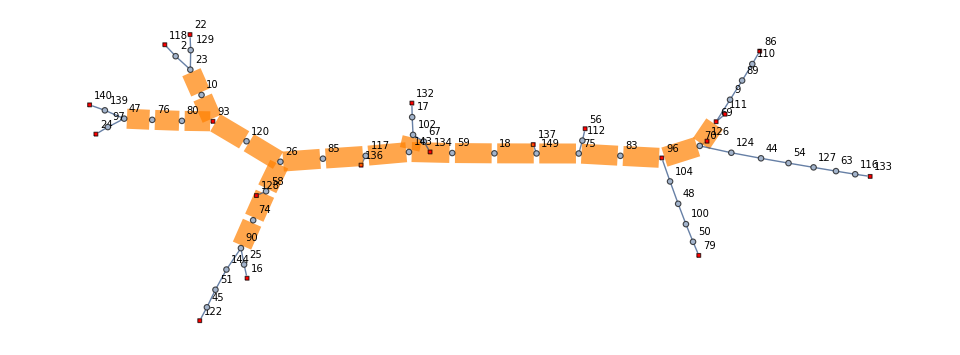

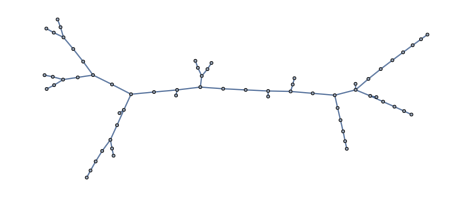

```mathematica
Graph@Join[{18<->149,18<->59,59<->143}, {70<->126,69<->70,70<->96,70<->124,9<->69,69<->111,83<->96,96<->104,44<->124,9<->89,75<->83,48<->104,44<->54,89<->110,75<->112,75<->149,48<->100,54<->127,86<->110,56<->112,137<->149,50<->100,63<->127,50<->79,63<->116,116<->133}, {85<->117,117<->136,117<->143,26<->85,102<->143,26<->58,26<->120,17<->102,67<->102,58<->74,58<->128,93<->120,17<->132,67<->134,74<->90,10<->93,80<->93,25<->90,90<->144,10<->23,76<->80,16<->25,51<->144,2<->23,23<->129,47<->76,45<->51,2<->118,22<->129,47<->97,47<->139,45<->122,24<->97,139<->140}]
```

```mathematica
res = Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"pathCosts"}]
```

{{117<->136,137<->149,24<->97,47<->97,47<->76,47<->139,76<->80,116<->133,63<->116,63<->127,26<->85,26<->120,26<->58,85<->117,117<->143,80<->93,93<->120,10<->93,22<->129,75<->149,18<->149,139<->140,86<->110,23<->129,89<->110,70<->126,69<->70,70<->96,70<->124,9<->69,69<->111,9<->89,83<->96,96<->104,75<->83,75<->112,44<->124,44<->54,54<->127,45<->122,45<->51,51<->144,90<->144,25<->90,74<->90,48<->104,48<->100,56<->112,16<->25,58<->74,58<->128,17<->132,17<->102,102<->143,67<->102,59<->143,50<->79,50<->100,67<->134,10<->23,2<->23,18<->59,2<->118},{{{{{47<->76,76<->80,80<->93},194,763},{{10<->23,10<->93},375,979},{{93<->120,26<->120},338,580},{{74<->90,58<->74},377,713},{{26<->58},321,321},{{26<->85,85<->117},210,554},{{102<->143},157,157},{{69<->70},161,161},{{70<->96},349,349},{{75<->149},397,397},{{117<->143},240,240}}}}}

```mathematica
res = Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"visiting"}]
```

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,96<->104}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149}

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149},{{{117,136,85,26,120,93,80,76,47,97,24,139,140,10,23,129,22,2,118,58,74,90,144,51,45,122,25,16,128,143,102,17,132,67,134,59,18,149,137,75,83,96,70,126,69,9,89,110,86,111,124,44,54,127,63,116,133,104,48,100,50,79,112,56}}}}

```mathematica
res = Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"root", "keyPath", "suc", "children", "parent"}]
```

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,96<->104}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149}

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149},{{{117}},{{{47<->76,76<->80,80<->93},{10<->23,10<->93},{93<->120,26<->120},{74<->90,58<->74},{26<->58},{26<->85,85<->117},{102<->143},{69<->70},{70<->96},{83<->96,75<->83},{75<->149},{18<->149,18<->59,59<->143},{117<->143}}},{{{136,85,143},{},{26},{120,58},{93},{80,10},{76},{47},{97,139},{24},{},{140},{},{23},{129,2},{22},{},{118},{},{74,128},{90},{144,25},{51},{45},{122},{},{16},{},{},{102,59},{17,67},{132},{},{134},{},{18},{149},{137,75},{},{83,112},{96},{70,104},{126,69,124},{},{9,111},{89},{110},{86},{},{},{44},{54},{127},{63},{116},{133},{},{48},{100},{50},{79},{},{56},{}}},{{DataStructure[FixedArray, {Data -> {Null, DataStructure[Stack, {Data -> {118}}], Null, Null, Null, Null, Null, Null, DataStructure[Stack, {Data -> {89}}], DataStructure[Stack, {Data -> {23}}], Null, Null, Null, Null, Null, <<127>>, DataStructure[Stack, {Data -> <<1>>}], DataStructure[Stack, {Data -> {51}}], Null, Null, Null, Null, DataStructure[Stack, {Data -> {137, 75}}], Null}}]}},{{DataStructure[FixedArray, {Data -> {Null, 23, Null, Null, Null, Null, Null, Null, 69, 93, Null, Null, Null, Null, Null, 25, 102, 59, Null, Null, Null, 129, 10, 97, 90, 85, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, <<88>>, Null, Null, 17, 116, 67, Null, 117, 149, Null, 47, 139, Null, Null, 117, 90, Null, Null, Null, Null, 18, Null}}]}}}}

```mathematica
gridResult[Graph@treeKouMarkowskyBerman100,  terminals100, Flatten@res⟦2,2,1⟧, edgeWeightSum[graph100, treeKouMarkowskyBerman100]]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 21343

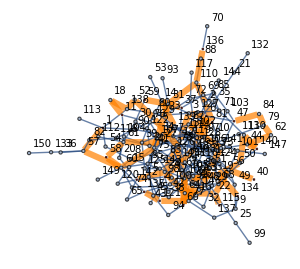
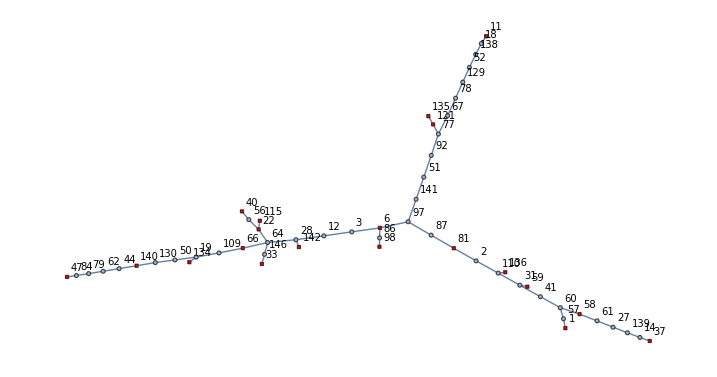
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 16406

```mathematica
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, edgeWeightSum[graph100, treeKouMarkowskyBerman100]]
```

```mathematica
{{{2<->110,2<->81,81<->87,87<->97},6<->110,6,110,{6<->110}},{{77<->92,51<->92,51<->141,97<->141},121<->77,121,77,{121<->77}},{{12<->28,3<->12,3<->6},64<->28,64,28,{64<->28}}}
```

### Key-Vertex Elimination

## Computations

```mathematica
test1=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{10, 15, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 1, False]
```

{{{{PLCHDR,PLCHDR},{10,15,3,WeightBounds→{1,100000}}},0.0060138},{{{PLCHDR,PLCHDR},{10,15,4,WeightBounds→{1,100000}}},0.0185274},{{{PLCHDR,PLCHDR},{10,15,5,WeightBounds→{1,100000}}},0.0517515},{{{PLCHDR,PLCHDR},{10,15,6,WeightBounds→{1,100000}}},0.114701},{{{PLCHDR,PLCHDR},{10,15,7,WeightBounds→{1,100000}}},0.270782}}

```mathematica
test2=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{100, 150, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 1, False]
```

{{{{PLCHDR,PLCHDR},{100,150,3,WeightBounds→{1,100000}}},0.599665},{{{PLCHDR,PLCHDR},{100,150,4,WeightBounds→{1,100000}}},1.27461},{{{PLCHDR,PLCHDR},{100,150,5,WeightBounds→{1,100000}}},2.94726},{{{PLCHDR,PLCHDR},{100,150,6,WeightBounds→{1,100000}}},6.49862},{{{PLCHDR,PLCHDR},{100,150,7,WeightBounds→{1,100000}}},14.6351}}

```mathematica
DumpSave[Directory[]~~"/dump/test_data.mx", {test1, test2}];
```

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {15, 3, BernoulliProbability->0.125}, 100, False]
```

0.0128711

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {100, 7, BernoulliProbability->0.1}, 1, False]
```

14.2756

```mathematica
testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {{15, 3, BernoulliProbability->0.125}, {50, 5, BernoulliProbability->0.08}, {100, 7, BernoulliProbability->0.05}}, 1, False]
```

{{{{PLCHDR,PLCHDR},{15,3,BernoulliProbability→0.125}},0.011905},{{{PLCHDR,PLCHDR},{50,5,BernoulliProbability→0.08}},0.760988},{{{PLCHDR,PLCHDR},{100,10,BernoulliProbability→0.05}},183.929}}

```mathematica
?runKouMarkowskyBerman
```

### SteinLib import

```mathematica
getInstancesList["\\steinlib\\D"]
```

{E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d01.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d02.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d03.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d04.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d05.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d06.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d07.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d08.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d09.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d10.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d11.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d12.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d13.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d14.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d15.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d16.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d17.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d18.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d19.stp,E:\Synch\Google\_Steiner_Tree_\Code\wolfram_steiner\steinlib\D\d20.stp}

```mathematica
getInstancesList["steinlib\\D"]
```

{steinlib\D\d01.stp,steinlib\D\d02.stp,steinlib\D\d03.stp,steinlib\D\d04.stp,steinlib\D\d05.stp,steinlib\D\d06.stp,steinlib\D\d07.stp,steinlib\D\d08.stp,steinlib\D\d09.stp,steinlib\D\d10.stp,steinlib\D\d11.stp,steinlib\D\d12.stp,steinlib\D\d13.stp,steinlib\D\d14.stp,steinlib\D\d15.stp,steinlib\D\d16.stp,steinlib\D\d17.stp,steinlib\D\d18.stp,steinlib\D\d19.stp,steinlib\D\d20.stp}

```mathematica
steinLibInstancesDList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\D"])⟦All, {1,3}⟧;
```

```mathematica
DumpSave[Directory[]~~"/dump/steinlib_D.mx", {steinLibInstancesDList}];
```

```mathematica
(*(steinLibInstancesDKou = tester[runKouMarkowskyBerman, steinLibInstancesDList, 10, First]);//AbsoluteTiming*)
```

```mathematica
(steinLibInstancesDMehlhorn = tester[runMehlhorn, steinLibInstancesDList, 1, First]);//AbsoluteTiming
```

{334.585,Null}

```mathematica
DumpSave[Directory[]~~"/dump/steinlib_D_sol.mx", {steinLibInstancesDMehlhorn}];
```

```mathematica
steinLibInfoD = Import["steinlib\\D_info.xlsx", "Data"]⟦1⟧;
steinLibInfoD = AssociationThread[Rest@First[steinLibInfoD], #]&/@Association[StringTrim[First[#]]->Rest[#]&/@Rest[steinLibInfoD]]
```

<|d01→<|vertices→1000 ,edges→1250 ,terminals→5 ,hardness→Ps ,opt→106 |>,d02→<|vertices→1000 ,edges→1250 ,terminals→10 ,hardness→Ps ,opt→220 |>,d03→<|vertices→1000 ,edges→1250 ,terminals→167 ,hardness→Ps ,opt→1565 |>,d04→<|vertices→1000 ,edges→1250 ,terminals→250 ,hardness→Ps ,opt→1935 |>,d05→<|vertices→1000 ,edges→1250 ,terminals→500 ,hardness→Ps ,opt→3250 |>,d06→<|vertices→1000 ,edges→2000 ,terminals→5 ,hardness→Ps ,opt→67 |>,d07→<|vertices→1000 ,edges→2000 ,terminals→10 ,hardness→Ps ,opt→103 |>,d08→<|vertices→1000 ,edges→2000 ,terminals→167 ,hardness→Ps ,opt→1072 |>,d09→<|vertices→1000 ,edges→2000 ,terminals→250 ,hardness→Ps ,opt→1448 |>,d10→<|vertices→1000 ,edges→2000 ,terminals→500 ,hardness→Ps ,opt→2110 |>,d11→<|vertices→1000 ,edges→5000 ,terminals→5 ,hardness→Pm ,opt→29 |>,d12→<|vertices→1000 ,edges→5000 ,terminals→10 ,hardness→Pm ,opt→42 |>,d13→<|vertices→1000 ,edges→5000 ,terminals→167 ,hardness→Ps ,opt→500 |>,d14→<|vertices→1000 ,edges→5000 ,terminals→250 ,hardness→Ps ,opt→667 |>,d15→<|vertices→1000 ,edges→5000 ,terminals→500 ,hardness→Ps ,opt→1116 |>,d16→<|vertices→1000 ,edges→25000 ,terminals→5 ,hardness→Pm ,opt→13 |>,d17→<|vertices→1000 ,edges→25000 ,terminals→10 ,hardness→Pm ,opt→23 |>,d18→<|vertices→1000 ,edges→25000 ,terminals→167 ,hardness→Ps ,opt→223 |>,d19→<|vertices→1000 ,edges→25000 ,terminals→250 ,hardness→Ps ,opt→310 |>,d20→<|vertices→1000 ,edges→25000 ,terminals→500 ,hardness→Ls ,opt→537.|>|>

```mathematica
#["opt"]&/@Values[steinLibInfoD]
```

{106 ,220 ,1565 ,1935 ,3250 ,67 ,103 ,1072 ,1448 ,2110 ,29 ,42 ,500 ,667 ,1116 ,13 ,23 ,223 ,310 ,537.}

```mathematica
steinLibInstancesDKou⟦All, 2, 1⟧
```

```mathematica
steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0742628,0.0716055,0.496357,0.46475,0.806477,0.133225,0.14015,0.54008,0.600467,0.74154,0.680775,1.23063,1.2919,1.61241,2.43838,43.4364,54.4403,61.6807,89.785,73.9169}

```mathematica
steinLibDVert = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
steinLibDEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoD])
steinLibDTerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

{1250,1250,1250,1250,1250,2000,2000,2000,2000,2000,5000,5000,5000,5000,5000,25000,25000,25000,25000,25000}

{5,10,167,250,500,5,10,167,250,500,5,10,167,250,500,5,10,167,250,500}

```mathematica
steinLibDOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

```mathematica
steinLibDMehlhornTime  = steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0742628,0.0716055,0.496357,0.46475,0.806477,0.133225,0.14015,0.54008,0.600467,0.74154,0.680775,1.23063,1.2919,1.61241,2.43838,43.4364,54.4403,61.6807,89.785,73.9169}

```mathematica
steinLibDMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesDList⟦All, 1⟧,steinLibInstancesDMehlhorn⟦All, 2, 2⟧}]
```

{107,237,1608,1978,3263,73,105,1125,1513,2133,31,42,524,690,1137,15,25,248,335,542}

```mathematica
steinerSolutionQ@@@Transpose[{steinLibInstancesDMehlhorn⟦All, 2, 2⟧, steinLibInstancesDList⟦All, 2⟧}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
steinLibDMehlhornSolErr = N@Thread[Divide[(steinLibDMehlhornSolValues-steinLibDOpt), steinLibDOpt]]
```

{0.00943396,0.0772727,0.027476,0.0222222,0.004,0.0895522,0.0194175,0.0494403,0.0448895,0.0109005,0.0689655,0.,0.048,0.0344828,0.0188172,0.153846,0.0869565,0.112108,0.0806452,0.00931099}

```mathematica
Grid[Transpose[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн", "%Ошибки ^-3", "Время (сек.)"}}~Join~(Transpose[{Keys@steinLibInfoD, steinLibDVert, steinLibDEdges, steinLibDTerm, steinLibDOpt, steinLibDMehlhornSolValues,Round[steinLibDMehlhornSolErr, N@10^-3], Round[steinLibDMehlhornTime, N@10^-1]}]⟦{1, 5, 10, 15, 19, 20}⟧)~Join~{{"Среднее", "-", "-", "-", "-", "-", Round[Mean@steinLibDMehlhornSolErr, N@10^-3], Round[Mean@steinLibDMehlhornTime, N@10^-1]}}],
Frame->All]
```

Задача | d01 | d05 | d10 | d15 | d19 | d20 | Среднее
#Вершин | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
#Ребер | 1250 | 1250 | 2000 | 5000 | 25000 | 25000 | -
#Терминалов | 5 | 500 | 500 | 500 | 250 | 500 | -
Оптимальное | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
Мельхорн | 107 | 3263 | 2133 | 1137 | 335 | 542 | -
%Ошибки ^-3 | 0.009 | 0.004 | 0.011 | 0.019 | 0.081 | 0.009 | 0.048
Время (сек.) | 0.1 | 0.8 | 0.7 | 2.4 | 89.8 | 73.9 | 16.7

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - nice paper

## ToDo List

```mathematica
"
- Эвристики для больших графов.
-- Жадные (old)
-- Локальный поиск (2010)
- Провести тесты
"

"
? - Точная постановка.
? - Алгоритм с 1.53 приближением.
? - Prunning and predprocessing.
? - Ускоренный на separation's DW (2007)

- Исправить восстановление дерева в DW ?????
"

"
Done:
- Melhorn
- Дописать в тестер возможность модельных данных
- Протестировать на модельных (библиотечных) данных.
"
```

```mathematica
circuit design,networking,and computational biology
```